# Virtual Particle Exchange Algorithm

This file contains source code of VPE localization algorithm and its application to shape formation.
Please put the WllTest.dll file in the same directory as this one.

## Generate robots’ position

equPoint is a function which allows you to create some approximately evenly-spaced points within a region.

```mathematica
equPoint[rego_,n_]:=With[{reg=N@rego},{points=n,samples=n*10,iterations=Round[15+10Log10[n]],regn=RegionNearest[reg]},Nest[With[{randoms=Join[#,RandomPoint[reg,samples]]},regn[Mean@randoms[[#]]&/@Values@PositionIndex@Nearest[#,randoms]]]&,RandomPoint[reg,points],iterations]]
```

Create 100 robots in a square shape.

```mathematica
robots=With[{s=10},equPoint[Rectangle[-.455s{1,1},.455s{1,1}],s^2]];
```

Plot the distribution of distance between adjacent robots.

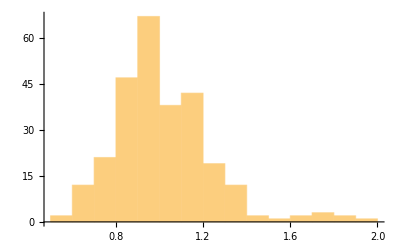

```mathematica
Histogram[Select[Norm[#1-#2]&@@@MeshPrimitives[DelaunayMesh[robots],{1}][[;;,1]],#<2&],20]
```

## Execute Localization

Functions used to create connectivity matrix T.

```mathematica
cm=LibraryFunctionLoad[NotebookDirectory[]<>"WllTest.dll","wll_creatematrix",{{Complex,1},Real,Real},LibraryDataType[SparseArray,Real,3]];
cXm=LibraryFunctionLoad[NotebookDirectory[]<>"WllTest.dll","wll_createXmatrix",{{Complex,1},Real,Real},LibraryDataType[SparseArray,Real,2]];

xymat[robots_,range_,k_,k0_]:=Module[{x,y},
{x,y}=cm[#1+I#2&@@Transpose@robots,range,k];
{SparseArray[Band[{1,1}]->(1-k0 Total/@x)]+k0 x,SparseArray[Band[{1,1}]->(1-k0 Total/@y)]+k0 y,SparseArray[Band[{1,1}]->(1-k0 Total@x)]+k0 Transpose@x,SparseArray[Band[{1,1}]->(1-k0 Total@y)]+k0 Transpose@y}
]
xmat[robots_,range_,k_,k0_]:=Module[{x},
x=cXm[#1+I#2&@@Transpose@robots,range,k];
{SparseArray[Band[{1,1}]->(1-k0 Total/@x)]+k0 x,SparseArray[Band[{1,1}]->(1-k0 Total@x)]+k0 Transpose@x}
]
```

Construct spare connectivity matrix.

```mathematica
{mx,my,mx1,my1}=xymat[robots,2.5,0.15,0.03];
```

Execute Localization!
dattemp is a list of localization result with x+ y+ x- y- as concerned direction.
locdat is the localization result in different iterations.

```mathematica
p=ConstantArray[1.,Length@robots];
dattemp=1.72Transpose[Function[x,Log[NestList[#.x&,p,500]]]/@{mx,my,mx1,my1},{3,1,2}]/2/.15;
locdat=(dattemp[[;;,;;,{1,2}]]-dattemp[[;;,;;,{3,4}]])/2;
```

Plot localization result

```mathematica
DrawError[pt_,loc_]:=With[{nloc=With[{m=Mean@loc-Mean@pt},#-m&/@loc]},Graphics[{PointSize@Large,Opacity@.3,Arrowheads@Small,Purple,Point/@pt,Darker@Darker@Green,Point/@nloc,Darker@Red,Arrow/@Thread[{pt,nloc}]},ImageSize->300]]
```

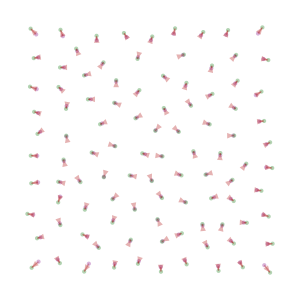

```mathematica
DrawError[robots,locdat[[-1]]]
```

## Shape Formation

Setup initial position of robots and the target region.

```mathematica
initial=;
reg=;
```

Do some pre-processing to the region.
Define attractive force component.

```mathematica
rb=RegionBoundary@reg;

ptf=RegionNearest[rb];
disf=SignedRegionDistance[reg];

regionf[pts_]:=With[{near=ptf/@pts,dis=disf/@pts},.07*(1+Tanh[dis/.12]) Sign[dis] (Normalize/@(near-pts)+1.*^-10)]
```

Begin Calculation!

```mathematica
Block[{mlist,robots=initial,pre,loc,tmp},

(*Create connectivity matrix*)
mlist=xymat[robots,0.5,0.15,0.01];

(*Execute initial localization*)
pre=MapThread[Function[{x,p},Nest[#.x&,p,100]],{mlist,ConstantArray[1.,{4,Length@robots}]}];

(*Now proceed to shape formation steps*)
shapeform=Table[
(*Generate connectivity matrix with the updated position of robots*)
mlist=xymat[robots,0.5,0.15,0.01];

(*Execute localization refinement*)
pre=MapThread[Function[{x,p},Nest[#.x&,p,10]],{mlist,pre}];

(*Get localization result*)
loc=0.35Transpose@Log[pre[[{1,2}]]/pre[[{3,4}]]]/.6;

(*remember the localization result and the position of robots*)
tmp={loc,robots};

(*Move robots!*)
robots+=
(*Repulsive component*)
.5Thread[With[{sigp=Total@ReplacePart[#1,{x_,x_}->0.],sign=Total@ReplacePart[#2,{x_,x_}->0.]},Thread[Tanh[10(Max/@Transpose@{sigp,sign}-.2)]((sigp-sign)/(sigp+sign))]]&@@@{mlist[[{1,3}]],mlist[[{2,4}]]}]
(*Attractive component*)
+1.regionf[loc];

tmp
,
{i,51}]
];
```

Aligning the centroid of robots to the centroid of the target shape.

```mathematica
With[{m=Mean@shapeform[[-1,2]]},shapeform[[;;,2]]=shapeform[[;;,2]]/.{x_Real,y_Real}:>{x,y}-m];
```

Plot position of robots and the localization error in the shape formation procedure.

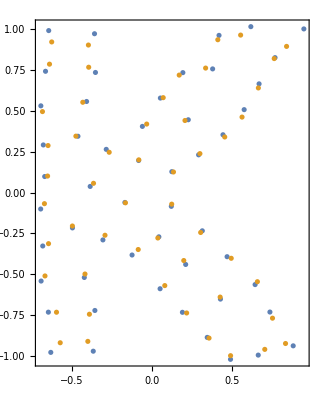

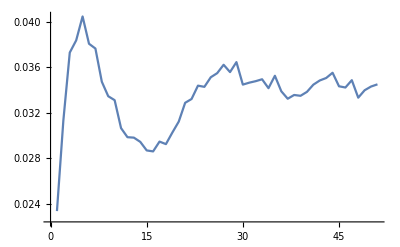

```mathematica
ListPlot[{shapeform[[-1,1]],shapeform[[-1,2]]},AspectRatio->Automatic,Frame->True,Axes->False]
ListLinePlot[Mean[Norm/@Abs[With[{s=shapeform[[#,1]]-shapeform[[#,2]]},#-Mean@s&/@s]]]&/@Range@Length@shapeform,PlotRange->Full]
```

Plot trace of robots

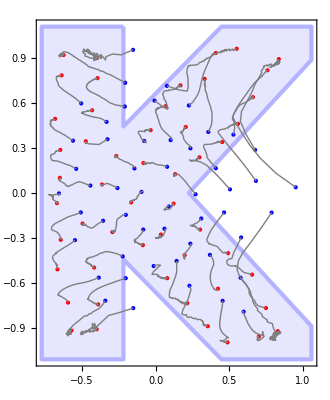

```mathematica
Graphics[{Lighter[Blue,.9],EdgeForm@Directive[Lighter[Blue,.7],AbsoluteThickness@3],reg,Blue,Point@shapeform[[1,2]],Red,Point@shapeform[[-1,2]],Gray,Line/@Thread@shapeform[[;;,2]]},AspectRatio->Automatic,Frame->True]
```